# Unstable CVTs and energy approach

## Initialization

```mathematica
Clear[regs]; 
regs=<|"Square"->BoundaryDiscretizeRegion@Rectangle[{-1,-1},{1,1}],
"Disk"->BoundaryDiscretizeRegion@Disk[]|>;


Clear[vMesh,cellsOrdered];
vMesh[pts_,regID_]:=With[{mesh=BoundaryDiscretizeRegion/@MeshPrimitives[VoronoiMesh[pts,{{-1,1},{-1,1}}],2],
reg=regs[regID]
},
RegionIntersection[#,reg]&/@mesh
];

(*Ordering cells with respect of seeds*)
cellsOrdered[cells_,pts_]:=cells[[SparseArray[Outer[#2@#1&,pts,RegionMember/@cells,1],
Automatic,False]["NonzeroPositions"][[All,2]]]];

tinyRegionPlot[arr_,regID_,size_]:= With[{mesh=vMesh[arr,regID]},
 Graphics[{EdgeForm@Gray,FaceForm@LightBlue,mesh,
	  PointSize@.04,Point@arr},ImageSize->size]]/;MemberQ[Keys[regs],regID];
```

Можно ввести условную энергию

ℰ = ∑_(i=1)^N ∫_cell_i (‖x-seed_i‖)^2 ⅆx

Ее минимумы достигаются для SCVTs (глобальный - для одного из них),
седловые точки - unstable CVTs. Чтобы найти критические точки, введем градиент:

∇ℰ =OverVector[2∫_cell_i (x-seed_i)ⅆx]=OverVector[2(centroid_i-seed_i)]

Минимизация градиента дает все CVT. 
Чтобы отделить седловые точки и реальные минимумы, необходим анализ хессиана.
TODO  Задать вопрос: точная формула, оптимальный численный подход

```mathematica
Clear[ℰ,𝒢,𝓃𝒢,ℋ,𝓈ℋ];

ℰ[seeds_,regID_]:=With[{cells=cellsOrdered[vMesh[seeds,regID],seeds]},
  Total@MapThread[
    ({x0,y0}=#1;NIntegrate[(x0-x)^2+(y0-y)^2,{x,y}∈#2])&,
   {seeds,cells}]]/;MatrixQ[seeds,NumericQ];
   
𝒢[seeds_,regID_]:=With[{centers=RegionCentroid/@cellsOrdered[vMesh[seeds,regID],seeds]},
  MapThread[(#1-#2)&,{seeds,centers}]]/;MatrixQ[seeds,NumericQ];
```

Минимизировать нужно сумму норм градиента

```mathematica
𝓃𝒢[seeds_,regID_]:=With[{centers=RegionCentroid/@cellsOrdered[vMesh[seeds,regID],seeds]},
  Total[Norm/@MapThread[(#1-#2)&,{seeds,centers}]]]/;MatrixQ[seeds,NumericQ];
```

Попытка численно оценить хессиан

```mathematica
shift[arr_,pos_,step_,regID_]:=ReplacePart[arr, 
  pos->RegionNearest[regs[regID],arr⟦pos⟧+step]];

ℋ[seeds_,δ_,regID_]:=(res={};
Do[
AppendTo[res,{0.5 (Flatten@𝒢[shift[seeds,i,{δ,0},regID],regID]-Flatten@𝒢[shift[seeds,i,{-δ,0},regID],regID])/δ,
0.5 (Flatten@𝒢[shift[seeds,i,{0,δ},regID],regID]-Flatten@𝒢[shift[seeds,i,{0,-δ},regID],regID])/δ}],
{i,Length@seeds}];res);
```

```mathematica
𝓈ℋ[seeds_,δ_,regID_]:=(g0=𝓃𝒢[seeds,regID];res={};
Do[
  AppendTo[res,{{𝓃𝒢[shift[seeds,i,{δ,0},regID],regID]-g0, 
    𝓃𝒢[shift[seeds,i,{-δ,0},regID],regID]-g0},
    {𝓃𝒢[shift[seeds,i,{0,δ},regID],regID]-g0,
     𝓃𝒢[shift[seeds,i,{0,-δ},regID],regID]-g0}}],
{i,Length@seeds}];res);

𝓈ℰ[seeds_,δ_,regID_]:=(e0=ℰ[seeds,regID];res={};
Do[
  AppendTo[res,{{ℰ[shift[seeds,i,{δ,0},regID],regID]-e0, 
    ℰ[shift[seeds,i,{-δ,0},regID],regID]-e0},
    {ℰ[shift[seeds,i,{0,δ},regID],regID]-e0,
     ℰ[shift[seeds,i,{0,-δ},regID],regID]-e0}}],
{i,Length@seeds}];res);
```

## Interactive VT

Press “Get data” button for to see energy and norm of gradient 
and store seeds in global variable gPts

```mathematica
(*Set number of seeds and region*)
numSeeds=4;regID="Square";

(*Global seeds coords*)gPts={};

DynamicModule[{pts=RandomPoint[regs[regID],numSeeds],mesh,centers,
Ε=None,Γ=None},
Row[{
LocatorPane[Dynamic[pts],
Dynamic[
mesh=cellsOrdered[vMesh[pts,regID],pts];
centers=RegionCentroid/@mesh;
Show[mesh,
Graphics[{Orange,PointSize[0.02],Point@centers}],
ImageSize->300]
],ContinuousAction->False],
Column[{
Button["Get data",
gPts=pts;
Ε=Total@MapThread[({x0,y0}=#1;NIntegrate[(x0-x)^2+(y0-y)^2,{x,y}∈#2])&,
   {pts,mesh}];
Γ =MapThread[(#1-#2)&,{pts,centers}](* Total[Norm/@MapThread[(#1-#2)&,{pts,centers}]]*)
],
Row[{"Energy  ",Dynamic@Ε}],
Row[{"Grad norm   ",Dynamic@Γ}]
},ItemSize->{20,Automatic}]
}]]
```

Вся проблема в том, что вручную мы находим не точный минимум (и не точную седловую точку)

```mathematica
𝓈ℰ[gPts,0.05,"Square"]
```

```mathematica
m=𝓈ℋ[gPts,0.02,"Square"]
```

```mathematica
Re[Eigenvalues[Flatten[m,1]]]
```

## Minimize gradient

TODO Но так находятся оба вида!!  Как искать только unstable??

```mathematica
Clear[p,numSeeds,var,cons];
numSeeds=4;regID="Square";
var=Array[p,{numSeeds,2}];
cons=And@@(#∈gRegs[regID]&/@var);
Clear[f,res,out];out={};
```

```mathematica
NMinimize[{res=𝓃𝒢[var,regID],cons},Flatten[var],
Method->{"RandomSearch","SearchPoints"->10,
 "RandomSeed"->RandomInteger[99999]},
EvaluationMonitor:>(out={res,var};If[res<0.01,Abort[]];Print["G = ",res])]
```

```mathematica
tinyRegionPlot[out[[2]],"Square",100]
```

## Energy relief

Центры берутся из ячейки с ручным построением. 
TODO Примеры рельефа для минимума и перегиба

-Graphics-

Векторы секущей плоскости выбираем вручную

```mathematica
Subscript[V, 1]=SparseArray[{{3,1}->1},{Length@gPts,2}];
Subscript[V, 2]=SparseArray[{{3,2}->1},{Length@gPts,2}];Normal @Subscript[V, 2]
```

```mathematica
bnds=Quiet@Reduce[And@@(#∈Rectangle[{-0.9,-0.9},{0.9,0.9}]&/@(gPts+α Subscript[V, 1]+β Subscript[V, 2])),{α,β},Reals]
```

```mathematica
ContourPlot[ℰ[gPts+α Subscript[V, 1]+β Subscript[V, 2],"Square"],
(*{α,-0.05,0.05},{β,-0.05,0.05},*)
{α,bnds⟦1,1⟧,bnds⟦1,5⟧},{β,bnds⟦2,1⟧,bnds⟦2,5⟧},
PerformanceGoal->"Speed",PlotRange->Full]
```

## Results

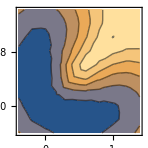
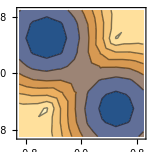
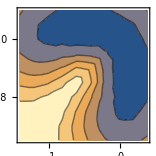
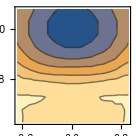
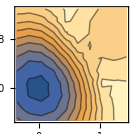
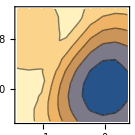
Три по диагонали -Graphics--Graphics- -Graphics-

Три SCVT     -Graphics-   -Graphics--Graphics-